```mathematica
SetDirectory["/Users/leonard/Documents/Projects/PhysicalDistance/Codes/kickedRotor"];
<<"kickedRotor.wl"
```

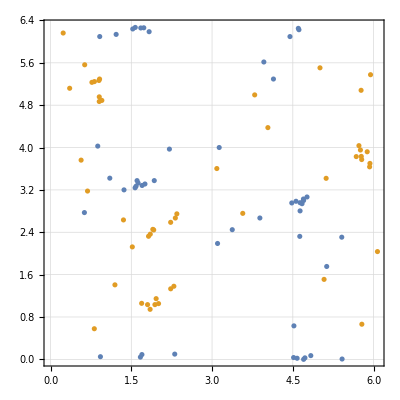

```mathematica
trajLen=50;
k=3.;
m=15;
thLis={{4.7,4.7+(2.π)/m}};
pLis={{3.,3+(2.π)/m}};
Do[
AppendTo[pLis,Mod[pLis[[-1]]+k*Sin[thLis[[-1]]],2.*π]];
AppendTo[thLis,Mod[thLis[[-1]]+pLis[[-1]],2.*π]];
(*AppendTo[pLis,pLis[[-1]]+k*Sin[thLis[[-1]]]];
AppendTo[thLis,thLis[[-1]]+pLis[[-1]]];*)
,{trajLen}];
tb=Table[Transpose[{thLis[[;;,i]],pLis[[;;,i]]}],{i,1,2}];
ListPlot[tb[[;;,1;;50]],{PlotTheme->"Detailed",AspectRatio->1,PlotRange->{0.,2.π}}]
```

```mathematica
l2Dis[x_,y_]:=Norm[(x-y)^2];
```

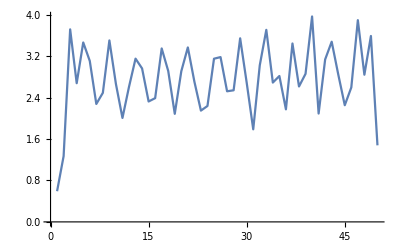

```mathematica
dis=Table[dist@@Transpose[z],{z,Transpose[{thLis,pLis}]}];
ListLinePlot[dis[[;;50]]]
```

```mathematica
FindFit[dis[[;;10]],dis[[1]]* Exp[a (t-1)],{a},t]
```

{a→0.368064}

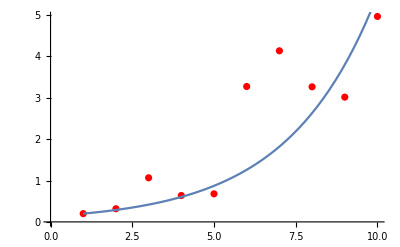

```mathematica
Show[ListPlot[dis⟦1;;10⟧,PlotStyle->Red],Plot[dis⟦1⟧ Exp[a (t-1)]/.{a->0.3680642447586771},{t,1,10}]]
```

```mathematica
dist[{1,1},{2,2}]
```

2

```mathematica
tb[[1,1]]
```

{4.7,3.}